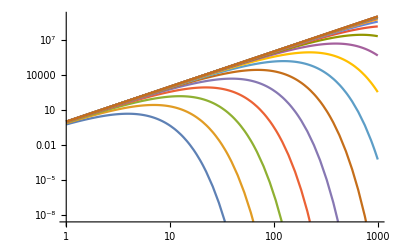

```mathematica
LogLogPlot[Evaluate[Table[w^4/(Exp[w/t]-1)/t,{t,10^Range[0,5,.25]}]],{w,1,10^3}]
```

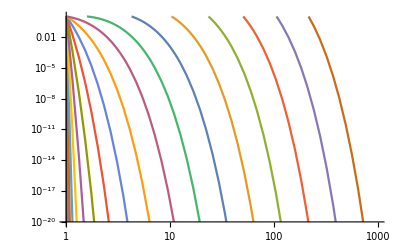

```mathematica
LogLogPlot[Evaluate[Table[w^4/(Exp[w/t]-1)Exp[1/t],{t,10^Range[-4,1,.25]}]],{w,1,10^3},PlotRange->{10^-20,1}]
```

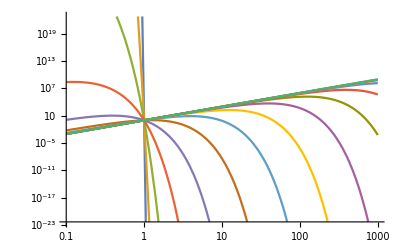

```mathematica
LogLogPlot[Evaluate[Table[w^4/(Exp[w/t]-1)/(1/(Exp[1/t]-1)),{t,10^Range[-3,4,.5]}]],{w,.1,10^3}]
```

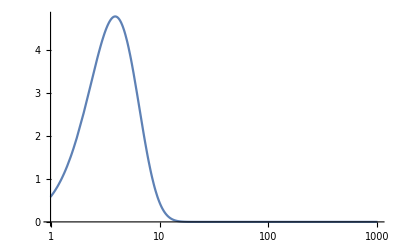

```mathematica
LogLinearPlot[w^4/(Exp[w]-1),{w,1,1000}]
```

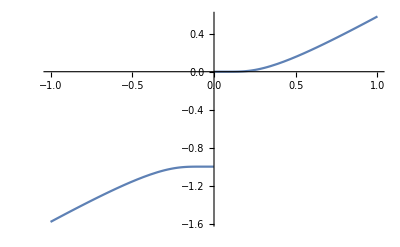

```mathematica
Plot[1/(Exp[1/x]-1),{x,-1,1}]
```